```mathematica
Clear["Global'*"]
D2R = Pi/180;
R2D = 180/Pi;
<<ToMatlab.m

$Assumptions={r>0};
```

```mathematica
(*--------------------------------------------------------------------------------*)
(* Looking for Nose Location *)

BfieldKSM = {Bx, By, Bz};
VswKSM = {-1, 0, 0};
NvecKSM = {1, 0, 0};
PB = Norm[Cross[NvecKSM, BfieldKSM]] + (1/2)*Dot[NvecKSM,VswKSM]//ComplexExpand

(* Bfield: Dipole, Untilted *)

MdipoleKSM=M*{0,0,-1};
PositionKSM = {r*Cos[theta], r*Sin[theta]*Cos[phi], r*Sin[theta]*Sin[phi]}; (*{r, theta, phi}: spherical coordinates relative to untilted KSM frame*)
ErKSM = PositionKSM / r;
BdipoleKSM = (1/r^3)*(3*Dot[MdipoleKSM,ErKSM]*ErKSM - MdipoleKSM);
PBDipole = PB /.{Bx->BdipoleKSM[[1]], By->BdipoleKSM[[2]],Bz->BdipoleKSM[[3]]}/.{theta->0, phi->0};

(* Bfield: Dipole, UnTilted, but Tilt=0 *)

RPhi = { { Cos[Phi], -Sin[Phi], 0 }, { Sin[Phi], Cos[Phi], 0 }, {0, 0,1 } };
RTheta = { { Cos[Theta], 0, Sin[Theta] }, { 0, 1, 0 }, {-Sin[Theta], 0, Cos[Theta] } };
Tilt = RPhi.RTheta;
MdipoleKSMTilt = Tilt.Transpose[{MdipoleKSM}]

MDotEr = MdipoleKSMTilt[[1]][[1]]*ErKSM[[1]] + MdipoleKSMTilt[[2]][[1]]*ErKSM[[2]]+MdipoleKSMTilt[[3]][[1]]*ErKSM[[3]];
MdipoleKSMTilt = { MdipoleKSMTilt[[1]][[1]],  MdipoleKSMTilt[[2]][[1]],  MdipoleKSMTilt[[3]][[1]]};
BdipoleKSMTilt =  (1/r^3)*(3*MDotEr*ErKSM - MdipoleKSMTilt);
PBDipoleTilt = PB /.{Bx->BdipoleKSMTilt[[1]], By->BdipoleKSMTilt[[2]],Bz->BdipoleKSMTilt[[3]]}/.{Theta->0, Phi->0}/.{phi->Pi/2}
```

-1/2+√(By^2+Bz^2)

{{-M Cos[Phi] Sin[Theta]},{-M Sin[Phi] Sin[Theta]},{-M Cos[Theta]}}

-1/2+√(((M-3 M Sin[theta]^2)^2)/r^6)

```mathematica
(* Solving PB *)
PBSimp = -1/2+(M-3 M Sin[theta]^2)/r[theta]^3;
Var={Sin[theta]^2 -> nu};
PBDipoleTilt/.Var;
EQ1 = (M-3 M nu)/r^3-1/2
EQ2 = D[PBSimp, theta]/.{r'[theta]->r*Tan[theta]}/.{r[theta]->r}/.Var/.{Sin[theta]->Sqrt[nu], Cos[theta]->Sqrt[1-nu], Tan[theta]->Sqrt[nu/(1-nu)]}
Solve[{EQ1==0, EQ2==0}, {r, nu}]
```

-1/2+(M-3 M nu)/r^3

-(6 M √(1-nu) √nu)/r^3-(3 √(nu/(1-nu)) (M-3 M nu))/r^3

{{r→-(-2)^(1/3) M^(1/3),nu→0},{r→2^(1/3) M^(1/3),nu→0},{r→(-1)^(2/3) 2^(1/3) M^(1/3),nu→0},{r→2 (-1/5)^(1/3) M^(1/3),nu→3/5},{r→-(2 M^(1/3))/5^(1/3),nu→3/5},{r→-(2 (-1)^(2/3) M^(1/3))/5^(1/3),nu→3/5}}

```mathematica
(* Bfield: Dipole, UnTilted, but Tilt>0 *)

PBDipoleTilt = PB /.{Bx->BdipoleKSMTilt[[1]], By->BdipoleKSMTilt[[2]],Bz->BdipoleKSMTilt[[3]]}/.{phi->Pi/2};

PBSimp = -1/2+Sqrt[M^2 Sin[Phi]^2 Sin[Theta]^2+(M Cos[Theta]+3 Sin[theta] (-M Cos[Theta] Sin[theta]-M Cos[Phi] Cos[theta] Sin[Theta]))^2]/r^3/.{r->X/Cos[theta]}//Simplify
Solve[PBSimp==0, X]

(*EQ1 =PBSimp/.{Sin[theta]->Sqrt[nu], Cos[theta]->Sqrt[1-nu], Cos[Phi]->CP, Sin[Phi]->SP, Cos[Theta]->CT, Sin[Theta]->ST}

EQ2 = D[PBSimp/.{r->r[theta]}, theta]/.{r'[theta]->r*Tan[theta]}/.{r[theta]->r}/.{ Tan[theta]->Sqrt[nu/(1-nu)], Sin[theta]->Sqrt[nu], Cos[theta]->Sqrt[1-nu], Cos[Phi]->CP, Sin[Phi]->SP, Cos[Theta]->CT, Sin[Theta]->ST}//Simplify

Solve[{EQ1==0, EQ2==0}, {r, nu}];*)
```

-1/2+(Cos[theta]^3 √(M^2 (Sin[Phi]^2 Sin[Theta]^2+(Cos[Theta] (-1+3 Sin[theta]^2)+3 Cos[Phi] Cos[theta] Sin[theta] Sin[Theta])^2)))/X^3

{{X→-(-2)^(1/3) Cos[theta] (M^2 (Sin[Phi]^2 Sin[Theta]^2+(Cos[Theta] (-1+3 Sin[theta]^2)+3 Cos[Phi] Cos[theta] Sin[theta] Sin[Theta])^2))^(1/6)},{X→2^(1/3) Cos[theta] (M^2 (Sin[Phi]^2 Sin[Theta]^2+(Cos[Theta] (-1+3 Sin[theta]^2)+3 Cos[Phi] Cos[theta] Sin[theta] Sin[Theta])^2))^(1/6)},{X→(-1)^(2/3) 2^(1/3) Cos[theta] (M^2 (Sin[Phi]^2 Sin[Theta]^2+(Cos[Theta] (-1+3 Sin[theta]^2)+3 Cos[Phi] Cos[theta] Sin[theta] Sin[Theta])^2))^(1/6)}}

```mathematica
FuncMax =M Cos[Theta]+3 Sin[theta] (-M Cos[Theta] Sin[theta]-M Cos[Phi] Cos[theta] Sin[Theta]);
Deriv = D[FuncMax, theta]/.{theta->ArcTan[X]};
Sol = Solve[Deriv==0,X]//Simplify;

X1 = X/.Sol[[1]]
X2 = X/.Sol[[2]]
Series[X1, {Theta, 0, 1}]
Series[X2, {Theta, 0, 1}]

X1ValRad = X1/.{Theta->27*Pi/180, Phi->40*Pi/180} 
ArcTan[X1ValRad]*180/Pi //N
```

Sec[Phi] (Cot[Theta]-Csc[Theta] √((Cos[Phi]^2+Cot[Theta]^2) Sin[Theta]^2))

Sec[Phi] (Cot[Theta]+Csc[Theta] √((Cos[Phi]^2+Cot[Theta]^2) Sin[Theta]^2))

-1/2 Cos[Phi] Theta+O[Theta]^2

(2 Sec[Phi])/Theta+1/6 (-4+3 Cos[Phi]^2) Sec[Phi] Theta+O[Theta]^2

(Cot[(3 π)/20]-√(Cos[(2 π)/9]^2+Cot[(3 π)/20]^2)) Sec[(2 π)/9]

-10.6608

```mathematica
(*Plot[{ArcTan[ X1/.{Theta->27*Pi/180}]*180/Pi, ArcTan[ X1/.{Theta->10*Pi/180}]*180/Pi, ArcTan[ X1/.{Theta->5*Pi/180}]*180/Pi},{Phi,0,Pi}]*)

(*Plot[{ArcTan[ X1/.{Theta->27*Pi/180}]*180/Pi, ArcTan[ X1/.{Theta->10*Pi/180}]*180/Pi, ArcTan[ X1/.{Theta->5*Pi/180}]*180/Pi},{Phi,0,Pi}]*)
(*phi = ArcCos[Sin[Theta]*Sin[Phi]]
*)
X = 20*Sin[ArcTan[ X1]]*Sin[Theta]*Sin[Phi]/.{Theta->27*Pi/180};
Y= 20*Sin[ArcTan[ X1]]*Sin[ArcCos[Sin[Theta]*Sin[Phi]]]/.{Theta->27*Pi/180};

(*
Table1 = Table[{X,Y}, {Phi,0,Pi,Pi/10}];*)
```

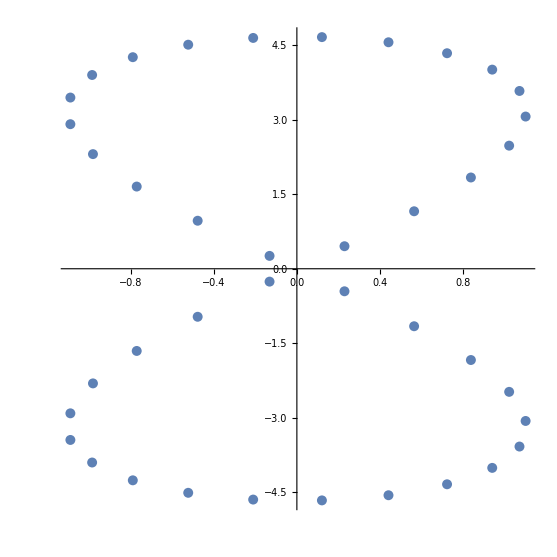

```mathematica
Table1 = Table[{X,Y}, {Phi,0.1,2*Pi,Pi/20}];

ListPlot[Table1, AspectRatio->1]
```

```mathematica
BfieldMB={BfieldKSM[[2]], BfieldKSM[[3]], BfieldKSM[[1]]};

MCartToSph = { {Sin[theta]*Cos[phi],  Sin[theta]*Sin[phi], Cos[theta] },
			{Cos[theta]*Cos[phi] , Cos[theta]*Sin[phi], -Sin[theta]},
		         {-Sin[phi],                          Cos[phi],                            0                      }
		       };
BfieldSpherical = MCartToSph.BfieldMB;
VswKSM = {-1, 0, 0};
VswMB = {VswKSM[[2]], VswKSM[[3]], VswKSM[[1]]};
VswSpherical = MCartToSph.VswMB;

NvecKSM = {1, 0, 0};
NvecSpherical =  MCartToSph.NvecKSM;

PB = Norm[Cross[NvecSph, BfieldSpherical]] + (1/2)*Dot[NvecSph,VswSpherical]//ComplexExpand;
```